# Ecuaciones en diferencias

```mathematica
sol=RecurrenceTable[{x[n+1]==Cosh[(x[n]-1)/2],x[0]==2},x,{n,0,10}];
```

```mathematica
apxy=Table[8*(1/8)^(2^n)+1,{n,0,10}];
```

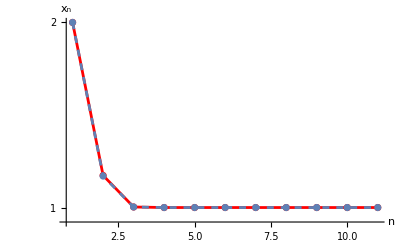

```mathematica
Show[{ListPlot[sol,Joined->True,Mesh->All,AxesLabel->{n,Subscript[x,n]},ScalingFunctions->"Log",PlotStyle->Red,PlotRange->All],ListPlot[apxy,Joined->True,Mesh->All,AxesLabel->{n,Subscript[x,n]},ScalingFunctions->"Log",PlotRange->All,PlotStyle->Dashed]}]
```

```mathematica
PlotRange->{{8,1000},{0.05,1}},
```

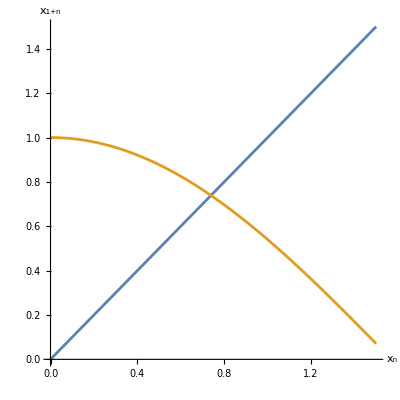

```mathematica
Plot[{x,Cos[x]},{x,0,1.5},PlotRange->{Automatic,{0,1.5}},AspectRatio->1,AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
sol1=RecurrenceTable[{x[n+1]==Cos[x[n]],x[1]==0},x,{n,15}];
```

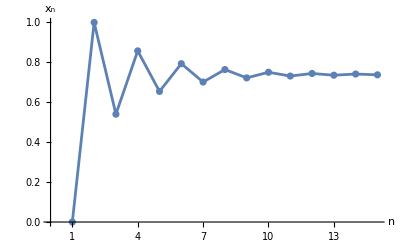

```mathematica
ListPlot[sol1,Joined->True,Mesh->All,AxesLabel->{n,Subscript[x,n]},Ticks->{Table[n,{n,15}],Automatic}]
```

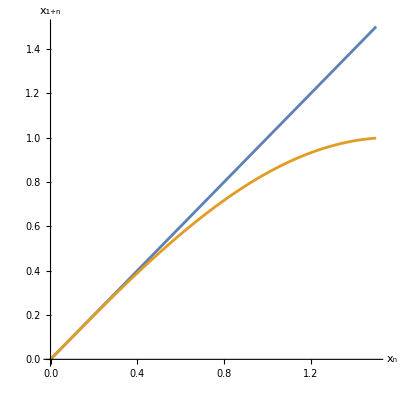

```mathematica
Plot[{x,Sin[x]},{x,0,1.5},PlotRange->{Automatic,{0,1.5}},AspectRatio->1,AxesLabel->{Subscript[x,n],Subscript[x,n+1]}]
```

```mathematica
sol2=RecurrenceTable[{x[n+1]==Sin[x[n]],x[1]==0.8},x,{n,1000}];
```

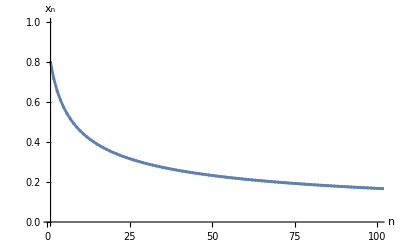

```mathematica
ListPlot[sol2,Joined->True,Mesh->All,PlotRange->{{1,100},{0,1}},AxesLabel->{n,Subscript[x,n]}]
```

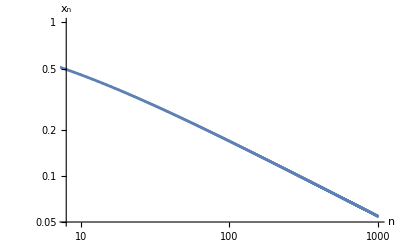

```mathematica
ListPlot[sol2,Joined->True,Mesh->All,PlotRange->{{8,1000},{0.05,1}},AxesLabel->{n,Subscript[x,n]},ScalingFunctions->{"Log","Log"}]
```